# Improving Time Series Model Fit With Variance Modeling

Adding a dynamic equation for conditional variance can improve model fit

Lawrence Temlock, June 28,  2018

A financial time series can be serially uncorrelated or have minor lower order serial correlations, but it can still be a dependent series.  As a result, discrete state - continuous time models such as autoregressive (AR), moving average (MA), ARMA and other model tools can underperform as analytical tools.

To improve model performance, it is possible to model conditional variance of the time series. In these cases, adding a dynamic equation with white noise to govern the time evolution of the return variance can improve the model’s fit, and explain the series’ dependencies beyond correlations.

This essay simply highlights the financial time series dependence phenomenon, with examples, and proposes there can be benefits in non-financial scientific research to test time series data sets for dependency, and construct appropriate models.  Not only in financial time series but in various other time series, a model incorporating conditional variance may seek to capture variance clusters, stochastic jumps, large price movement leverage effects, logarithmically-scaled evolution, and fat-tailed distributions.

## The problem: Serially dependent asset returns

Returns of financial assets may show weak or no correlations in their time series, but may still be conditionally dependent on their past values.   To identify and measure this, we can apply the Ljung-Box test for autocorrelation to the residuals series, or alternatively apply the Lagrange multiplier test of Engle.

Consider the time series returns of IBM stock, and the S&P 500, and their descriptive statistics:

```mathematica
(*  Plot IBM and SP 500 returns  *)

IBM$fData   = FinancialData["IBM","Return",{{2011,1,1},{2018,2,20}},"Value"];
IBM$returns = TimeSeries[IBM$fData,{{2011,1,1},Automatic,"BusinessDay"},HolidayCalendar->{"UnitedStates","NYSE"},TemporalRegularity->True];
len$IBM = Length[IBM$fData];
IBM$level = 2/(Sqrt[IBM$returns["PathLength"]]);
IBM$Sq$level = 2/IBM$returns["PathLength"];
```

```mathematica
SP$fData   = FinancialData["^SPX","Return",{{2011,1,1},{2018,2,20}},"Value"];
SP$returns = TimeSeries[SP$fData,{{2011,1,1},Automatic,"BusinessDay"},HolidayCalendar->{"UnitedStates","NYSE"},TemporalRegularity->True];
len$SP = Length[SP$fData];
SP$level = 2/(Sqrt[SP$returns["PathLength"]]);
SP$Sq$level = 2/SP$returns["PathLength"];
```

```mathematica
TabView[{
DateListPlot[IBM$returns,ImageSize->500,PlotRange->All],
DateListPlot[SP$returns,ImageSize->500,PlotStyle->Red,PlotRange->All]
}]
```

12

The returns have nearly zero mean, are somewhat left-skewed, and have fat tails.

```mathematica
(* show descriptive statistics *)
IBM$logr$sample$mean = Mean[IBM$fData];
IBM$logr$sample$STD = StandardDeviation[IBM$fData];
IBM$logr$sample$skew = Skewness[IBM$fData];
IBM$logr$sample$kurtosis = Kurtosis[IBM$fData]-3;

SP$logr$sample$mean = Mean[SP$fData];
SP$logr$sample$STD = StandardDeviation[SP$fData];
SP$logr$sample$skew = Skewness[SP$fData];
SP$logr$sample$kurtosis = Kurtosis[SP$fData]-3;
```

```mathematica
(*  Plot histograms  *)

TableForm[{{IBM$logr$sample$mean, IBM$logr$sample$STD, IBM$logr$sample$skew, IBM$logr$sample$kurtosis}, 
          {SP$logr$sample$mean, SP$logr$sample$STD, SP$logr$sample$skew, SP$logr$sample$kurtosis}}, 
          TableHeadings -> {{"IBM", "S&P 500"}, {"Mean", "STD", "Skew", "Ex. Kurtosis"}}]
```

| Mean | STD | Skew | Ex. Kurtosis
IBM | 0.000208669 | 0.0119862 | -0.455644 | 6.42766
S&P 500 | 0.000463852 | 0.00902536 | -0.508016 | 5.30393

```mathematica
(*  Plot histograms  *)

TabView[{Histogram[IBM$fData,{0.001},PDF,ImageSize->500,PlotLabel->"Distribution of IBM Stock Monthly Returns"],
Histogram[SP$fData,{0.001},PDF,ImageSize->500,PlotLabel->"Distribution of S&P 500 Index Monthly Returns"]}]
```

12

Inspection of the individual series’ autocorrelation functions suggest that the log returns aren’t serially correlated.

```mathematica
(* plot autocorrelation functions *) 
    
TabView[{
    Manipulate[
    ListPlot[CorrelationFunction[IBM$returns,{2,n}],
    Filling->Axis,Joined->True,PlotStyle->Blue, ImageSize->500,PlotLabel->"IBM Autocorrelation Function (ACF)",
    PlotRange->{-0.10,0.10},Epilog->{Dashed,Line[{{0,IBM$level},{n,IBM$level}}],Line[{{0,-IBM$level},{n,-IBM$level}}]}],
    {n,5,100,1},SaveDefinitions->True],
    Manipulate[
    ListPlot[CorrelationFunction[SP$returns,{2,n}],
    Filling->Axis,Joined->True,PlotStyle->Red, ImageSize->500,PlotLabel->"SP 500 Autocorrelation Function (ACF)",
    PlotRange->{-0.10,0.10},Epilog->{Dashed,Line[{{0,SP$level},{n,SP$level}}],Line[{{0,-SP$level},{n,-SP$level}}]}],
    {n,5,100,1},SaveDefinitions->True]
    
    }]
```

12

The "n" slider determines the number of autocorrelation lags shown in the chart.

Inspection of the autocorrelation functions for the squared log returns and the absolute log returns suggest the likelihood of series dependency.

```mathematica
(* plot autocorrelation functions *)
IBMAbsRtPlot = Manipulate[
	ListPlot[CorrelationFunction[Abs[IBM$returns],{2,n}],
	Filling->Axis,ImageSize->500,Joined->True,PlotRange->{0,All},PlotLabel->"ACF of IBM Absolute Returns"],
	{n,5,100,1},SaveDefinitions->True];

IBMSqRtPlot = Manipulate[
	ListPlot[CorrelationFunction[IBM$returns^2,{2,n}],
	Filling->Axis,ImageSize->500,Joined->True,PlotRange->{0,All},PlotRange->All,PlotLabel->"ACF of IBM Squared Returns",
	Epilog->{Dashed,Line[{{0,IBM$Sq$level},{n,IBM$Sq$level}}]}],
	{n,5,100,1},SaveDefinitions->True];

SPAbsRtPlot = Manipulate[
	ListPlot[CorrelationFunction[Abs[SP$returns],{2,n}],
	Filling->Axis,ImageSize->500,PlotStyle->Red,Joined->True,PlotRange->{0,All},PlotRange->All,PlotLabel->"ACF of SP 500 Absolute Returns"],
	{n,5,100,1},SaveDefinitions->True];

SPSqRtPlot = Manipulate[
	ListPlot[CorrelationFunction[SP$returns^2,{2,n}],
	Filling->Axis,ImageSize->500,PlotStyle->Red,Joined->True,PlotRange->{0,All},PlotRange->All,PlotLabel->"ACF of SP 500 Squared Returns",
	Epilog->{Dashed,Line[{{0,SP$Sq$level},{n,SP$Sq$level}}]}],
	{n,5,100,1},SaveDefinitions->True];
```

```mathematica
TabView[{
	IBMAbsRtPlot,
	IBMSqRtPlot,SPAbsRtPlot, SPSqRtPlot
	}]
```

1234

To test for series dependency, the Ljung-Box multiplier test applied to the residuals and squared residuals.   The p-values of the test statistics demonstrate mathematically that there is no significant correlation in the original time series residuals, but there is dependency as shown in the p-values for the squared residuals series.

```mathematica
(*  Show autocorrelations functions for residuals *)

Print["Time series residuals"]

TabView[{
	AutocorrelationTest[IBM$returns,Automatic,{"TestDataTable",All}],
	AutocorrelationTest[SP$returns,Automatic,{"TestDataTable",All}]
	}]
```

Time series residuals

12

Tab 1: IBM.  Tab 2: S&P 500

```mathematica
(*  Show autocorrelations functions for squared residuals *)

Print["Time series squared residuals"]

TabView[{
	AutocorrelationTest[IBM$returns^2,Automatic,{"TestDataTable",All}],
	AutocorrelationTest[SP$returns^2,Automatic,{"TestDataTable",All}]
	}]
```

Time series squared residuals

12

Tab 1: IBM.  Tab 2: S&P 500

If we fit a linear discrete time-continuous state other econometric model to the time series, the model will have dependencies not seen in the original data.

Consider the example of a moving-average model created using the function EstimatedProcess:

```mathematica
(* build GARCH models *)
Clear[v,a,p,b,q]


Print["Estimated IBM Moving Average Model"]
IBM$ARMA = EstimatedProcess[IBM$returns,MAProcess[{a,b},v]]

Print["Estimated S&P 500 Moving Average Model"]
SP$ARMA = EstimatedProcess[SP$returns,MAProcess[{a,b},v]]

IBM$ARMA$tsm = RandomFunction[IBM$ARMA,{0,100}]^2;

SP$ARMA$tsm = RandomFunction[SP$ARMA,{0,100}]^2;
```

Estimated IBM AR Model

MAProcess[{0.0280489,-0.0260193},0.000143378]

Estimated S&P 500 AR Model

MAProcess[{-0.048157,0.0211556},0.0000811871]

A test of the squared returns series generated by the model, applying the Ljung-Box Q*(m) statistic, indicates that serial dependence exists in some of the lags 5  - 30, for both IBM and the S&P 500 index:

ACF functions of the squared returns for the AR models

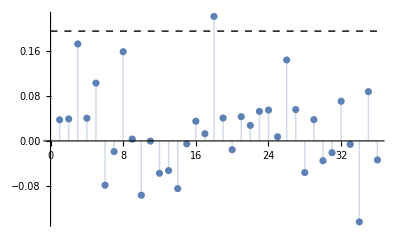
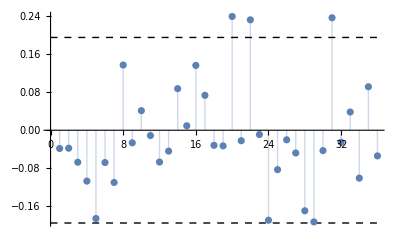

```mathematica
(*  Show ACF charts for the AR models *)

Print["ACF functions of the squared returns for the AR models"]
{IBM$ARMA$tsm["ACFPlot"], SP$ARMA$tsm["PACFPlot"]}
```

## Solution: Adding a conditional volatility equation to the model

A variety of conditional variance models have been proposed in academia and among finance professionals.  In general, models either use an exact function to govern the evolution of σ_t^2, or use a stochastic equation to describe σ_t^2.  Here we test a model of the first type, the GARCH model, for improved fit / reduced serial dependency compared to the prior MA model.

The GARCH models for IBM and the S&P 500 monthly returns are:

```mathematica
(* build GARCH models *)
Clear[v,a,p]


Print["Estimated IBM GARCH Model"]
IBM$GARCH = EstimatedProcess[IBM$returns,GARCHProcess[v,{a},{p}]]

Print["Estimated S&P 500 GARCH Model"]
SP$GARCH = EstimatedProcess[SP$returns,GARCHProcess[v,{a},{p}]]

IBM$tsm = RandomFunction[IBM$GARCH,{0,100}]^2;

SP$tsm = RandomFunction[SP$GARCH,{0,100}]^2;
```

Estimated IBM GARCH Model

GARCHProcess[0.000035409,{0.101763},{0.657513}]

Estimated S&P 500 GARCH Model

GARCHProcess[4.17848×10^-6,{0.174606},{0.773637}]

A test of the residuals applying the Ljung-Box Q*(m) statistic with the new GARCH mean indicates that serial dependence in lags 5 - 30 has been removed:

ACF functions of the squared returns for the GARCH models

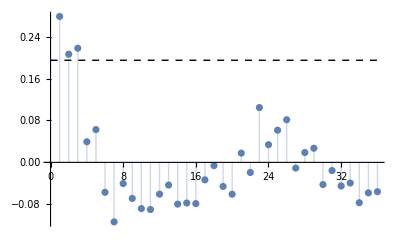
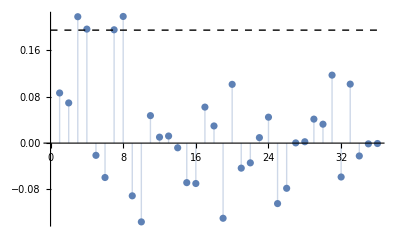

```mathematica
(*  Show ACF charts for the GARCH models *)

Print["ACF functions of the squared returns for the GARCH models"]
{IBM$tsm["ACFPlot"], SP$tsm["PACFPlot"]}
```

## Further explorations

The simple examples above can be expanded to include a variety of alternative conditional variance models, apropos to the asset type and financial market in question.   Further explorations could include a categorization of models for different asset types, including descriptive statistics and measurements of goodness of model fit.  Multivariate, vector autoregressive models can be explored for multiple assets in a portfolio.

It may also be interesting to include the Lagrange test to confirm results from the Ljung-Box method.  The Lagrange test is equivalent to the F statistic for testing α_i= 0 for  i = 1, ... ,m in the linear regression a_t^2 = α_0 + α_1a_(t-1)^2 + ... + α_ma_(t-m)^2 + e_t,  with t = m + 1 , ... , T, where  e_t denotes the error term, m is a prespecified positive integer, and T is the sample size.  The null hypothesis is H_0 : α_1 ==  ... == α_m==  0.  For each iteration, after the linear regression is completed, the components of the test ratio are computed:  SSR_0 = ∑_(t = m+1)^T (a_t^2 - (ω))^2, ω = (1/T) ∑_(t = 1)^T (a_t^2) is the sample mean of a_t^2,  SSR_1=  ∑_(t = m+1)^T  e_t^2 where e_t^2is the least squares residual of the prior linear regression, and F = ((SSR_0 -  SSR_1) / m)/(SSR_1/(T - 2m - 1)) which is asymptotically distributed as a chi-squared distribution with m degrees of freedom under the null hypothesis.

## Author contact information

lawrencetemlock@gmail.com